SparseArray[…]

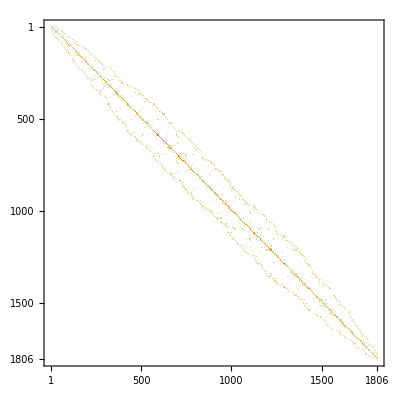

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc2/bcsstk14.mtx.gz"]
MatrixPlot[A]
```

```mathematica
63454./1806^2
```

0.0194547

```mathematica
AbsoluteTiming[
U=CholeskyDecomposition[A];
]
MatrixPlot[U]
AbsoluteTiming[Norm[A-Transpose[U].U]/Norm[A]]
```

{0.068931,Null}

-Graphics-

{2.95673,2.46382×10^-16}

```mathematica
b=SparseArray[{3->4.2,2->8.9},5]
Normal[b]
```

SparseArray[…]

{0,8.9,4.2,0,0}